```mathematica
Solve[x^3-1==0,x]
```

{{x→1},{x→-(-1)^(1/3)},{x→(-1)^(2/3)}}

```mathematica
NSolve[x^3-1==0,x]
```

{{x→-0.5-0.866025 ⅈ},{x→-0.5+0.866025 ⅈ},{x→1.}}

```mathematica
f[x_] := x^3 - 1;  
df[x_] := 3*x^2;  
Simplify[x - f[x]/df[x]]
```

1/(3 x^2)+(2 x)/3

```mathematica
(*Newton Fractal x^3-1=0*)
```

```mathematica
newt = Compile[{{z, _Complex}}, 
      Arg[FixedPoint[1/ (3 #^2 )+ 2 # /3 &, z, 35]]];
```

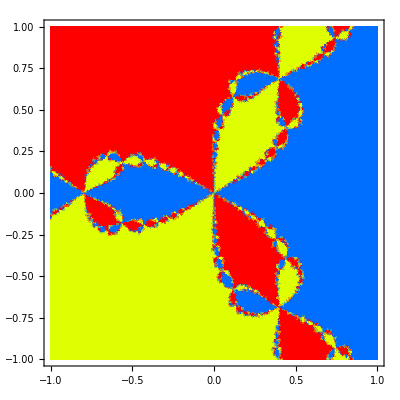

```mathematica
DensityPlot[newt[a+b I],
{a,-1,1},
{b,-1,1},
Mesh->False,DisplayFunction->Identity,PlotRange->All,PlotPoints->80,ColorFunction->Hue]
```

```mathematica
(*Julia集合*)

Julia[x_, y_, max_]:=(

c=0.285+0.01I;
z = x+I y; n=0; 
While[Abs[z]<2&& n< max, 
z = z^2+c; 
n++]; 
Return[n];)
DensityPlot[Julia[x,y,100],{x,-1.2,1.2},{y,-1.2,1.2},
Mesh->False,AspectRatio->Automatic,
PlotPoints->100,ColorFunction->Hue]
```

-Graphics-

```mathematica
(*Mandelbrot集合*)
```

```mathematica
Mandelbrot[x_, y_, max_]:=(
c= x+I y; n=0; z=0;
While[Abs[z]<2&& n< max, 
z = z^2+c; 
n++]; 
Return[n];
)
DensityPlot[Mandelbrot[x,y,100],{x,-2,0.5},{y,-1.5,1.5},
Mesh->False,AspectRatio->Automatic,
PlotPoints->100,ColorFunction->Hue]
```

-Graphics-